# Graph Colorings

Peter Burbery

Abstract

## Vertex Colorings

To color the vertices of a graph, no adjacent vertices can be the same color.

Make the function ColorGraphVertices a persistent function:

```mathematica
ResourceFunction["PersistResourceFunction"][{"PersistResourceFunction","ColorGraphVertices"}];
```

Color the vertices of the Petersen graph:

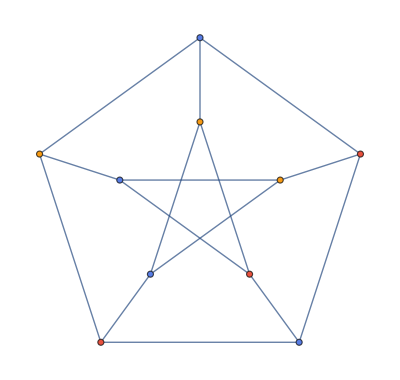

```mathematica
ColorGraphVertices[PetersenGraph[]]
```

Color the vertices of a random graph:

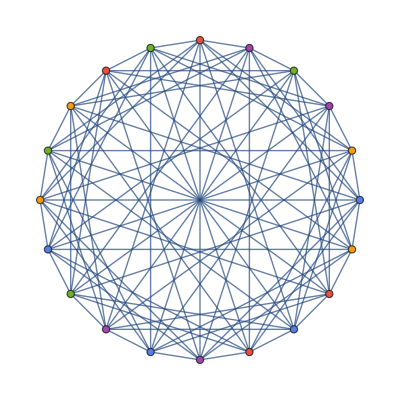

```mathematica
ColorGraphVertices[GraphData@@RandomSample[GraphData[],1]]
```

Make a gallery of graphs with colorings:

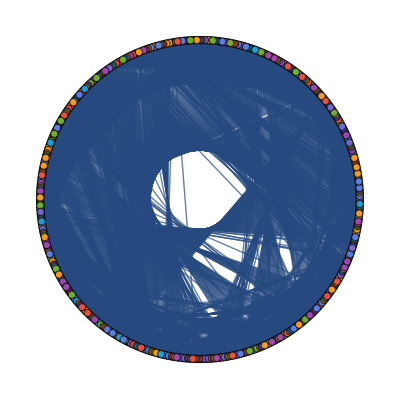
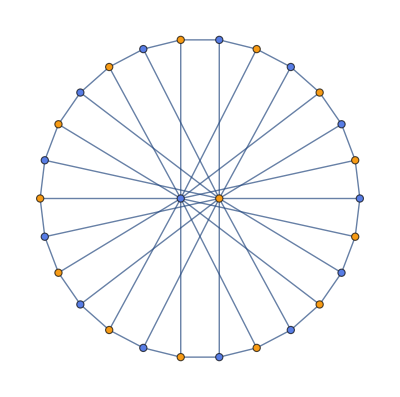
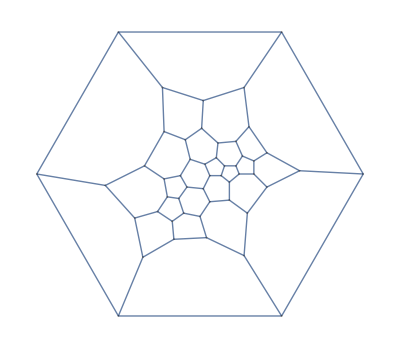
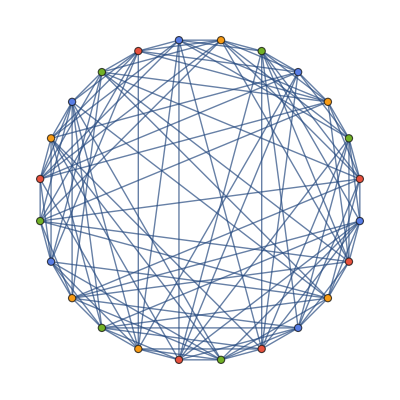
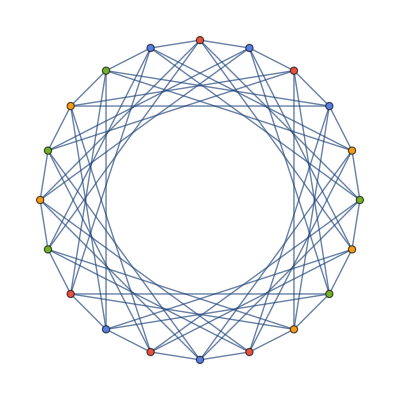
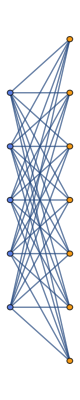
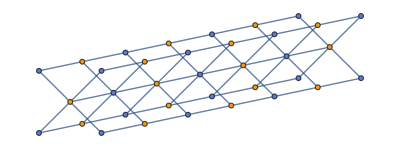
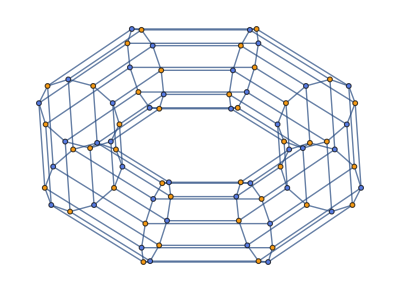

```mathematica
Select[GraphQ][ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],10])]
```

Deploy a gallery of colorings to the web:

```mathematica
CloudDeploy[GalleryView[Select[GraphQ][ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],48])]]]
```

CloudObject[https://www.wolframcloud.com/obj/173c4f6c-b542-464e-b923-8a8d74bc824b]

See information about the deployment:

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/obj/8685ca23-bb13-4147-b11a-900444f9cee1"]]
```

CloudObject: 8685ca23-bb13-4147-b11a-900444f9cee1

## Edge Colorings

```mathematica
PersistResourceFunction[{"ColorGraphEdges"}]
```

{Success[…]}

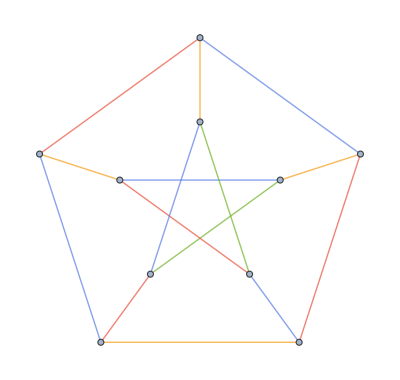

```mathematica
ColorGraphEdges[PetersenGraph[]]
```

Color the vertices of a random graph:

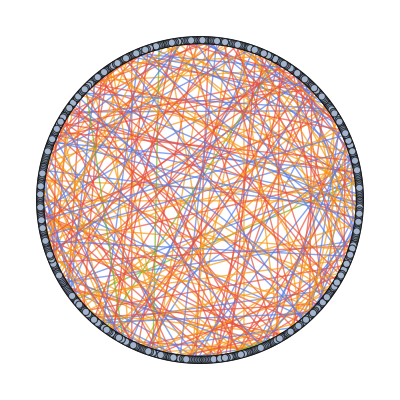

```mathematica
ColorGraphEdges[GraphData@@RandomSample[GraphData[],1]]
```

Make a gallery of graphs with colorings:

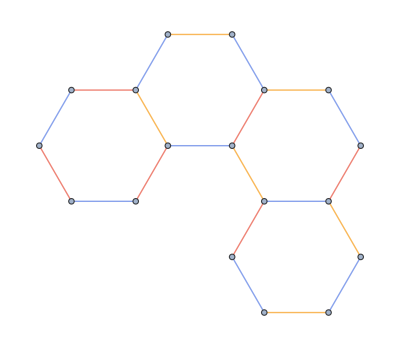
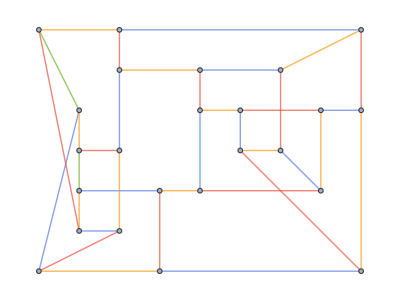
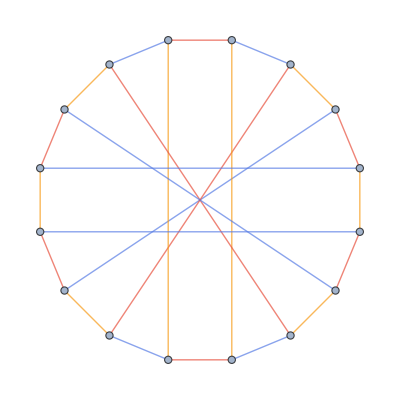
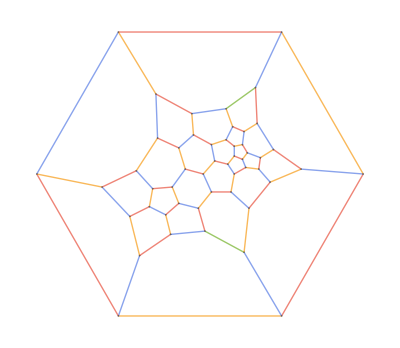
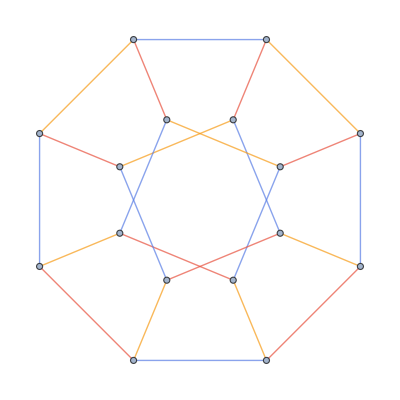
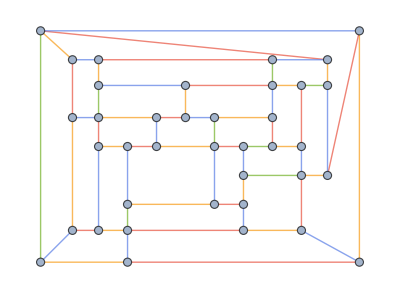
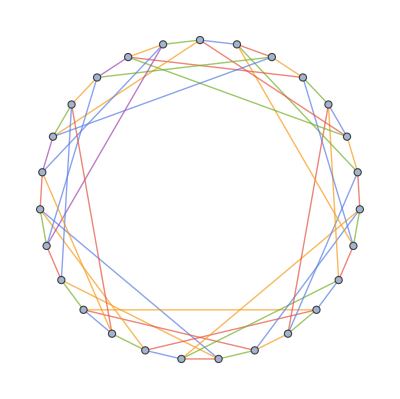
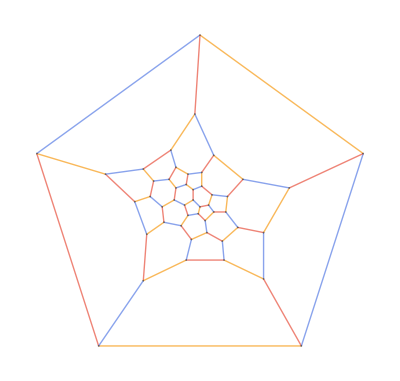

```mathematica
Select[GraphQ][ColorGraphEdges/@(GraphData/@RandomSample[GraphData[],10])]//Quiet
```

Another 10 graphs:

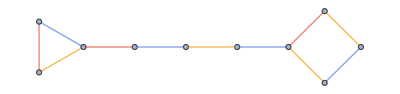
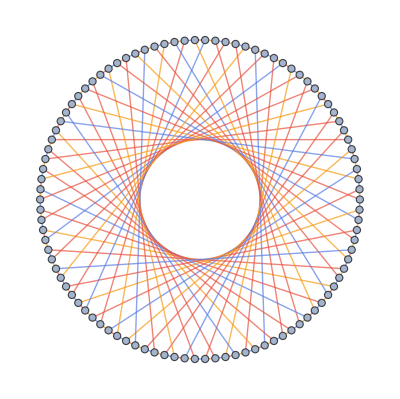
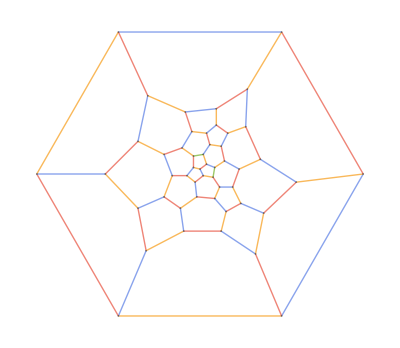
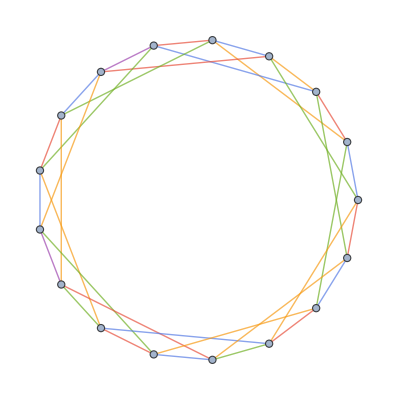
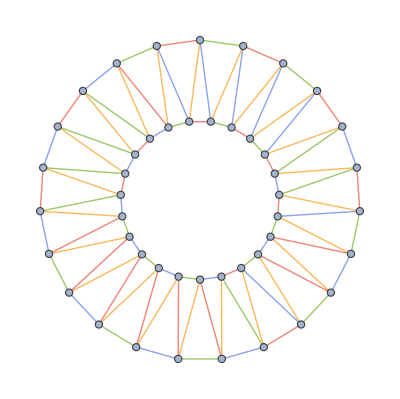
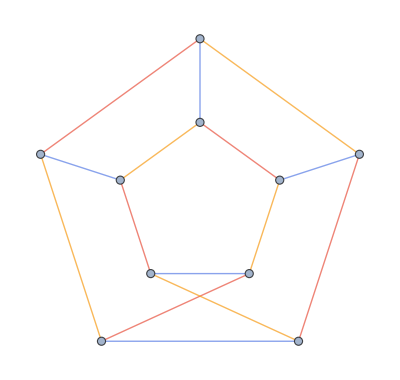
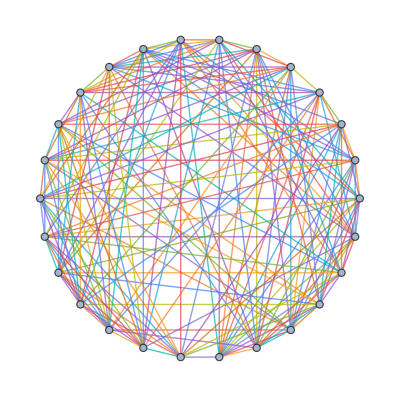
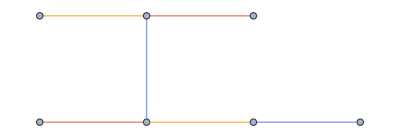

```mathematica
Select[GraphQ][ColorGraphEdges/@(GraphData/@RandomSample[GraphData[],10])]
```

```mathematica
CloudDeploy[GalleryView[Select[GraphQ][ColorGraphVertices/@(GraphData/@RandomSample[GraphData[],48])]]]
```

CloudObject[https://www.wolframcloud.com/obj/39138e3f-b3f7-4784-849e-ee33643ceec4]

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/obj/39138e3f-b3f7-4784-849e-ee33643ceec4"]]
```

CloudObject: 39138e3f-b3f7-4784-849e-ee33643ceec4

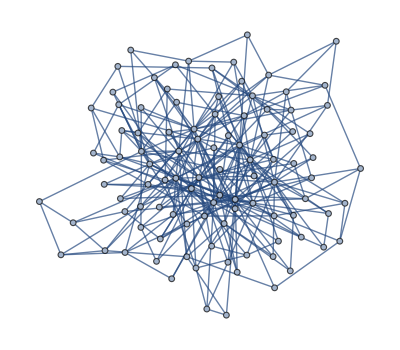

```mathematica
RandomGraph[BarabasiAlbertGraphDistribution[100,3]]
```

Each color represents a sports team:

```mathematica
RandomColor[10]
```

{RGBColor[0.7822737468590399, 0.4325395136794601, 0.20443806805645326],RGBColor[0.9441326689241614, 0.562131245999312, 0.24471925319837418],RGBColor[0.007933911816875083, 0.6836843417126091, 0.8142570055589504],RGBColor[0.1342078623441887, 0.17311592084504634, 0.8405856890638479],RGBColor[0.9325186487774355, 0.17092427262326582, 0.03101246654322276],RGBColor[0.06324186731132642, 0.4467083135884544, 0.883513215530493],RGBColor[0.5851779460267446, 0.019172729154533386, 0.9698824280194653],RGBColor[0.4252453642572467, 0.8797489200143258, 0.15963282861271222],RGBColor[0.25547035794952144, 0.6807497243450418, 0.711841420570283],RGBColor[0.4624617945074494, 0.4514585331634695, 0.9562665642676011]}

```mathematica
?RandomColor
```

```mathematica
RandomColor[10,2]
```

RandomColor::bdmdl: 10 is not a valid model specification. Models can be specified through color directives patterns.

RandomColor[10,2]

```mathematica
RandomColor[LUVColor[_,_,_],{10,2}]
```

{{LUVColor[0.07387873413502422, -0.2772832473285378, -0.006741086507493943],LUVColor[0.6386720742639997, 0.7843317829452587, -1.2402297243293385]},{LUVColor[0.8195579710805887, 0.03717083784097541, 0.7180346715808072],LUVColor[0.8760766987164474, 0.06389674696175396, -0.3430916413009246]},{LUVColor[0.7350993637957224, 0.16797095732618583, 1.133004111897094],LUVColor[0.8046215851617036, 1.045315238345716, -0.284939855311237]},{LUVColor[0.3755696384416476, -0.5653643732397686, 0.04975180022680448],LUVColor[0.4975857464761917, 0.08758284912027214, -0.4690183971694246]},{LUVColor[0.2054705820493825, 0.5301136973372378, 1.2927348732901693],LUVColor[0.14310948684152658, -0.35988963300148713, -1.0037186739605932]},{LUVColor[0.7434489913026923, -0.43603876727074553, -0.8703704237950305],LUVColor[0.9408737163004777, -0.807621196135345, 0.2717395150647315]},{LUVColor[0.5666425130775727, -0.012221967054602878, -0.5914748366687244],LUVColor[0.7461801518616098, -0.9550931123124276, 0.5934922054261893]},{LUVColor[0.21907519443591084, 1.2342706819511058, -1.2835091357233765],LUVColor[0.11557421208215501, -0.24348406911191, 0.5271987788000674]},{LUVColor[0.8928239935604785, 0.6524431979999381, 1.09436733502507],LUVColor[0.525412595745097, -0.9095651809345036, -0.67390665637279]},{LUVColor[0.9851083491114803, 0.26378699399302796, -0.5291657808327335],LUVColor[0.21768318180269253, 0.43928899950338973, 0.5118943859083958]}}

## Examples

A university has a number of different subjects. Each student is enrolled in some of these subjects. Build a graph where every vertex is a subject and an edge between two vertices means there is a common student:

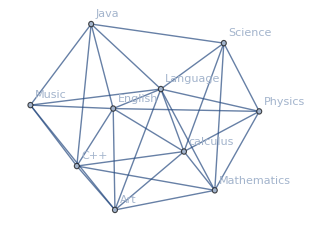
```mathematica
g=-Graphics-;
```

```mathematica
FullForm[g]
```

Graph[List["Java","C++","Science","calculus","Art","Mathematics","English","Music","Language","Physics"],List[UndirectedEdge["Java","C++"],UndirectedEdge["Java","Science"],UndirectedEdge["Java","English"],UndirectedEdge["Java","Music"],UndirectedEdge["Java","Language"],UndirectedEdge["C++","calculus"],UndirectedEdge["C++","Art"],UndirectedEdge["C++","Mathematics"],UndirectedEdge["C++","English"],UndirectedEdge["C++","Music"],UndirectedEdge["Science","calculus"],UndirectedEdge["Science","Mathematics"],UndirectedEdge["Science","Language"],UndirectedEdge["Science","Physics"],UndirectedEdge["calculus","Art"],UndirectedEdge["calculus","Mathematics"],UndirectedEdge["calculus","English"],UndirectedEdge["calculus","Language"],UndirectedEdge["calculus","Physics"],UndirectedEdge["Art","Mathematics"],UndirectedEdge["Art","English"],UndirectedEdge["Art","Music"],UndirectedEdge["Art","Language"],UndirectedEdge["Mathematics","Language"],UndirectedEdge["Mathematics","Physics"],UndirectedEdge["English","Music"],UndirectedEdge["English","Language"],UndirectedEdge["English","Physics"],UndirectedEdge["Music","Language"],UndirectedEdge["Language","Physics"]],List[Rule[FormatType,TraditionalForm],Rule[ImageSize,List[310.455,Automatic]],Rule[VertexLabels,List["Name"]]]]

```mathematica
ExpressionTree[g]
```

-Graphics-

```mathematica
ExpressionTree[First[g]]
```

First::normal: Nonatomic expression expected at position 1 in ….

-Graphics-

```mathematica
First[g]
```

First::normal: Nonatomic expression expected at position 1 in ….

First[-Graphics-]

```mathematica
TreeGraph[g]
```

TreeGraph[-Graphics-]

```mathematica
Names["*tree",IgnoreCase->True]
```

{ClusteringTree,CompleteKaryTree,CSGRegionTree,ExpressionTree,FindSpanningTree,GraphTree,KaryTree,NestTree,RandomTree,RootTree,RulesTree,Tree,UnlabeledTree}

```mathematica
GraphTre
```

```mathematica
GraphTree[-Graphics-]
```

GraphTree::tree: Valid tree graph expected at position 1 in ….

GraphTree[-Graphics-]

```mathematica
SimpleGraph[-Graphics-]
```

-Graphics-

```mathematica
GraphTree[SimpleGraph[-Graphics-]]
```

GraphTree::tree: Valid tree graph expected at position 1 in ….

GraphTree[-Graphics-]